```mathematica
ldot = α*l*(1-l-r);
rdot = α*r*(1-l-r);

sol = Solve[{ldot == 0, rdot == 0},{l, r}];

J = {{α*(1-r-2*l), -l*α},{-β*r, β*(1-l-2*r)}};
FullSimplify[J/.sol[[1]]]
FullSimplify[Tr[J]/.sol[[1]]]
FullSimplify[Det[J]/.sol[[1]]]

FullSimplify[Eigenvalues[J/.sol[[1]]]]
FullSimplify[Eigenvectors[J/.sol[[1]]]]
```

{{-l α,-l α},{(-1+l) β,(-1+l) β}}

-l α+(-1+l) β

0

{0,-l α+(-1+l) β}

{{-1,1},{(l α)/(β-l β),1}}

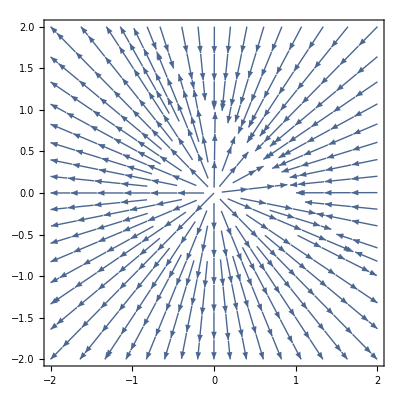

```mathematica
alpha = 1;
beta = 1;
ldot = alpha*l*(1-l-r);
rdot = beta*r*(1-l-r);
StreamPlot[{ldot,rdot},{l,-2,2},{r,-2,2}]
```

```mathematica
rdot = r*(1-A*r^rho-r)
```